## Active polymer driven by inhomogeneous excitations

This notebook illustrates the effects of active processes (either a diagonal correlation function with sinusoidal activity modulations or a box-shaped correlation function) on the polymer dynamics.

Load required packages.

```mathematica
Once@AppendTo[$Path,NotebookDirectory[]<>"Source/Diffusion/"];
Needs["DiffusionDiagonal`"->None,"ActivityModulations.wl"];
Needs["DiffusionBox`"->None,"CorrelatedExcitations.wl"];
```

Calculate mean squared traveled distance, based on activity modulations:

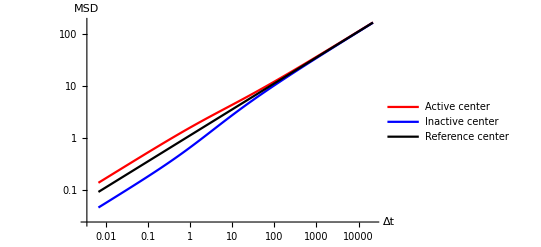

```mathematica
ListLogLogPlot[
{
Table[{Exp@x,DiffusionDiagonal`SquaredDistanceActive[0,Exp@x,0.5,1]},{x,-5,10,0.1}],
Table[{Exp@x,DiffusionDiagonal`SquaredDistanceActive[0,Exp@x,-0.5,1]},{x,-5,10,0.1}],
Table[{Exp@x,DiffusionDiagonal`SquaredDistanceActive[0,Exp@x,0,1]},{x,-5,10,0.1}]
},PlotLegends->{"Active center","Inactive center","Reference center"},
Joined->True,
PlotStyle->{Red,Blue,Black},
AxesLabel->{"Δt","MSD"}
]
```

Calculate mean squared traveled distance, based on correlated excitations:

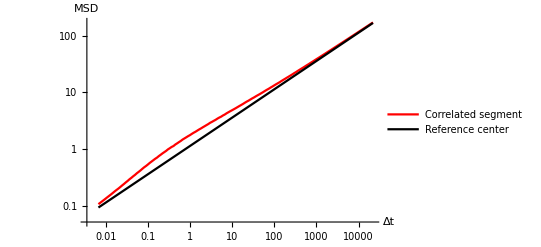

```mathematica
ListLogLogPlot[
{
Table[{Exp@x,DiffusionBox`SquaredDistanceActive[Exp@x,1,1]},{x,-5,10,0.1}],
Table[{Exp@x,DiffusionDiagonal`SquaredDistanceActive[0,Exp@x,0,1]},{x,-5,10,0.1}]
},PlotLegends->{"Correlated segment","Reference center"},
Joined->True,
PlotStyle->{Red,Black},
AxesLabel->{"Δt","MSD"}
]
```

Compare inhomogeneous contribution of active model driven by modulations in activity, and corresponding passive model:

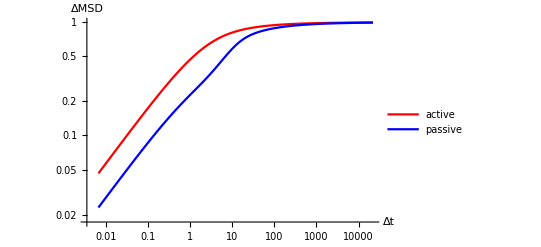

```mathematica
ListLogLogPlot[
{
Table[{Exp@x,DiffusionDiagonal`CorrectionActive[Exp@x]},{x,-5,10,0.1}],
Table[{Exp@x,DiffusionDiagonal`CorrectionPassive[Exp@x]},{x,-5,10,0.1}]
},PlotLegends->{"active","passive"},
Joined->True,
PlotStyle->{Red,Blue},
AxesLabel->{"Δt","ΔMSD"}
]
```

Compare inhomogeneous contribution of active model driven by correlated excitations, and corresponding passive model:

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00028576 and 6.06745×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000341361 and 6.5876×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000432281 and 6.86655×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

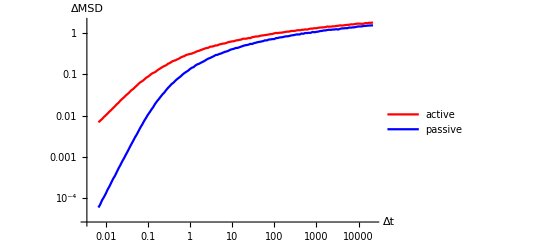

```mathematica
ListLogLogPlot[
{
Table[{Exp@x,DiffusionBox`CorrectionActive[Exp@x]},{x,-5,10,0.1}],
Table[{Exp@x,DiffusionBox`CorrectionPassive[Exp@x]},{x,-5,10,0.1}]
},PlotLegends->{"active","passive"},
Joined->True,
PlotStyle->{Red,Blue},
AxesLabel->{"Δt","ΔMSD"}
]
```